```mathematica
ClearAll["`*"];
```

1

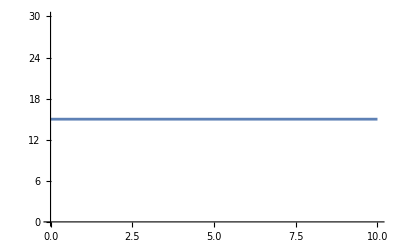

```mathematica
Subscript[K, 0]=2;
Subscript[K, 2]=2;
N0=5;
Length@Select[FullSimplify[NSolve[0==μ*Subscript[x, 1]+N0*Subscript[x, 2]*Subscript[x, 3]-Subscript[K, 0]*Subscript[x, 1]^3-Subscript[K, 2]*Subscript[x, 1]*(Subscript[x, 2]^2+Subscript[x, 3]^2)&&0==μ*Subscript[x, 2]+N0*Subscript[x, 1]*Subscript[x, 3]-Subscript[K, 0]*Subscript[x, 2]^3-Subscript[K, 2]*Subscript[x, 2]*(Subscript[x, 1]^2+Subscript[x, 3]^2)&&0==μ*Subscript[x, 3]+N0*Subscript[x, 2]*Subscript[x, 1]-Subscript[K, 0]*Subscript[x, 3]^3-Subscript[K, 2]*Subscript[x, 3]*(Subscript[x, 2]^2+Subscript[x, 1]^2),{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]],And@@(PossibleZeroQ[Im[#]]&)/@Values[#]&]
Plot[Length@Select[FullSimplify[NSolve[0==μ*Subscript[x, 1]+N0*Subscript[x, 2]*Subscript[x, 3]-Subscript[K, 0]*Subscript[x, 1]^3-Subscript[K, 2]*Subscript[x, 1]*(Subscript[x, 2]^2+Subscript[x, 3]^2)&&0==μ*Subscript[x, 2]+N0*Subscript[x, 1]*Subscript[x, 3]-Subscript[K, 0]*Subscript[x, 2]^3-Subscript[K, 2]*Subscript[x, 2]*(Subscript[x, 1]^2+Subscript[x, 3]^2)&&0==μ*Subscript[x, 3]+N0*Subscript[x, 2]*Subscript[x, 1]-Subscript[K, 0]*Subscript[x, 3]^3-Subscript[K, 2]*Subscript[x, 3]*(Subscript[x, 2]^2+Subscript[x, 1]^2),{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]],And@@(PossibleZeroQ[Im[#]]&)/@Values[#]&],{μ,0,10}]
```

```mathematica
vecField[x_,y_,z_]:={κ1*(μ*x+N0*y*z+K0*x^3+K2*x*(y^2+z^2)),κ2*(μ*y+N0*x*z+K0*y^3+K2*y*(x^2+z^2)),κ3*(μ*z+N0*x*y+K0*z^3+K2*z*(x^2+y^2))}
L={{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},
{D[vecField[x,y,z],x][[1]],D[vecField[x,y,z],y][[1]],D[vecField[x,y,z],z][[1]],c*κ1,0,0},
{D[vecField[x,y,z],x][[2]],D[vecField[x,y,z],y][[2]],D[vecField[x,y,z],z][[2]],0,c*κ2,0},
{D[vecField[x,y,z],x][[3]],D[vecField[x,y,z],y][[3]],D[vecField[x,y,z],z][[3]],0,0,c*κ3}}//FullSimplify
Eigenvalues[L/.{x->Sqrt[-μ/K0],y->0,z->0}]//FullSimplify
MatrixForm[L]
```

{{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{κ1 (3 K0 x^2+K2 (y^2+z^2)+μ),(2 K2 x y+N0 z) κ1,(N0 y+2 K2 x z) κ1,c κ1,0,0},{(2 K2 x y+N0 z) κ2,κ2 (3 K0 y^2+K2 (x^2+z^2)+μ),(N0 x+2 K2 y z) κ2,0,c κ2,0},{(N0 y+2 K2 x z) κ3,(N0 x+2 K2 y z) κ3,κ3 (K2 (x^2+y^2)+3 K0 z^2+μ),0,0,c κ3}}

{1/2 (c κ1-√κ1 √(c^2 κ1-8 μ)),1/2 (c κ1+√κ1 √(c^2 κ1-8 μ)),1/K0 Root[K0^3 N0^2 κ2 κ3 μ+K0^4 κ2 κ3 μ^2-2 K0^3 K2 κ2 κ3 μ^2+K0^2 K2^2 κ2 κ3 μ^2+(2 c K0^3 κ2 κ3 μ-2 c K0^2 K2 κ2 κ3 μ) #1+(c^2 K0^2 κ2 κ3-K0^2 κ2 μ+K0 K2 κ2 μ-K0^2 κ3 μ+K0 K2 κ3 μ) #1^2+(-c K0 κ2-c K0 κ3) #1^3+#1^4&,1],1/K0 Root[K0^3 N0^2 κ2 κ3 μ+K0^4 κ2 κ3 μ^2-2 K0^3 K2 κ2 κ3 μ^2+K0^2 K2^2 κ2 κ3 μ^2+(2 c K0^3 κ2 κ3 μ-2 c K0^2 K2 κ2 κ3 μ) #1+(c^2 K0^2 κ2 κ3-K0^2 κ2 μ+K0 K2 κ2 μ-K0^2 κ3 μ+K0 K2 κ3 μ) #1^2+(-c K0 κ2-c K0 κ3) #1^3+#1^4&,2],1/K0 Root[K0^3 N0^2 κ2 κ3 μ+K0^4 κ2 κ3 μ^2-2 K0^3 K2 κ2 κ3 μ^2+K0^2 K2^2 κ2 κ3 μ^2+(2 c K0^3 κ2 κ3 μ-2 c K0^2 K2 κ2 κ3 μ) #1+(c^2 K0^2 κ2 κ3-K0^2 κ2 μ+K0 K2 κ2 μ-K0^2 κ3 μ+K0 K2 κ3 μ) #1^2+(-c K0 κ2-c K0 κ3) #1^3+#1^4&,3],1/K0 Root[K0^3 N0^2 κ2 κ3 μ+K0^4 κ2 κ3 μ^2-2 K0^3 K2 κ2 κ3 μ^2+K0^2 K2^2 κ2 κ3 μ^2+(2 c K0^3 κ2 κ3 μ-2 c K0^2 K2 κ2 κ3 μ) #1+(c^2 K0^2 κ2 κ3-K0^2 κ2 μ+K0 K2 κ2 μ-K0^2 κ3 μ+K0 K2 κ3 μ) #1^2+(-c K0 κ2-c K0 κ3) #1^3+#1^4&,4]}

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
κ1 (3 K0 x^2+K2 (y^2+z^2)+μ) | (2 K2 x y+N0 z) κ1 | (N0 y+2 K2 x z) κ1 | c κ1 | 0 | 0
(2 K2 x y+N0 z) κ2 | κ2 (3 K0 y^2+K2 (x^2+z^2)+μ) | (N0 x+2 K2 y z) κ2 | 0 | c κ2 | 0
(N0 y+2 K2 x z) κ3 | (N0 x+2 K2 y z) κ3 | κ3 (K2 (x^2+y^2)+3 K0 z^2+μ) | 0 | 0 | c κ3)

```mathematica
A={{D[vecField[x,y,z],x][[1]],D[vecField[x,y,z],y][[1]],D[vecField[x,y,z],z][[1]]},
{D[vecField[x,y,z],x][[2]],D[vecField[x,y,z],y][[2]],D[vecField[x,y,z],z][[2]]},
{D[vecField[x,y,z],x][[3]],D[vecField[x,y,z],y][[3]],D[vecField[x,y,z],z][[3]]}}/.{y->x,z->x}
A.{{c*κ1,0,0},{0,c*κ2,0},{0,0,c*κ3}}-{{c*κ1,0,0},{0,c*κ2,0},{0,0,c*κ3}}.A//FullSimplify//MatrixForm
```

{{κ1 (3 K0 x^2+2 K2 x^2+μ),(N0 x+2 K2 x^2) κ1,(N0 x+2 K2 x^2) κ1},{(N0 x+2 K2 x^2) κ2,κ2 (3 K0 x^2+2 K2 x^2+μ),(N0 x+2 K2 x^2) κ2},{(N0 x+2 K2 x^2) κ3,(N0 x+2 K2 x^2) κ3,κ3 (3 K0 x^2+2 K2 x^2+μ)}}

(0 | c x (N0+2 K2 x) κ1 (-κ1+κ2) | c x (N0+2 K2 x) κ1 (-κ1+κ3)
c x (N0+2 K2 x) (κ1-κ2) κ2 | 0 | c x (N0+2 K2 x) κ2 (-κ2+κ3)
c x (N0+2 K2 x) (κ1-κ3) κ3 | c x (N0+2 K2 x) (κ2-κ3) κ3 | 0)